# Example # 3 : Generic Hybrid Undulator/Wiggler (no side magnet, M misalignment, rtg, for)

Version 0.7

## Introduction

This example creates and solves a simple multipole wiggler made with rectangular blocks. It is important to execute each section in the order of presentation. If not, errors may be reported. Any section can be edited and executed several times. To see the change in the peak field induced by the variation of the magnet size, edit the corresponding parameter in the section entitled "Create the Geometry", execute this section and re-execute the section "Solve". The section "Optimizing Parameters" provides an example of manual optimization of the pole dimensions.
To obtain acceptable precision on the magnetic field, it is essential to increase the segmentation. This is done at the expense of memory and CPU time. The segmentation in this example has been set to np={2,2,5} for the pole and nm={1,3,1} for the magnet. This corresponds to an absolute error in the peak field of the undulator/wiggler of the order of 1%. The user himself should experience consequences of   increasing np and nm and see how CPU time and memory increase, and how the value of the peak field approaches a limit which is the value looked for. To do so, edit the nm or np values in the "Create the Geometry" section, and re-execute both the "Create the Geometry" and "Solve" sections. Using segmentation which is too large segmentation may result in a memory allocation failure. To recover from such situation, the section "Load and Initialize Radia" should be re-executed. Memory allocation failure can be avoided (to some extent) by giving more memory to the Radia.exe process (Macintosh). 
It is a fact that iron pieces need much more segmentation than the magnets since the magnetization there is very sensitive to the external field.
One can also compute the Field Integral produced by such an undulator/wiggler, forces on the magnets and poles, etc. One can build a wedge pole undulator by using polyhedrons or extruded polygons instead of rectangular blocks... To learn more, read the Radia documentation, make tests and develop experience.

## Load and Initialize Radia

The following instruction loads the Radia package and returns the Radia version number. This notebook requires the Radia version 4.097 or later.

```mathematica
<<Radia`;
(* if Vector field plot is required *)
<<VectorFieldPlots`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

General::obspkg: VectorFieldPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Define Magnetic Material

The following instructions define a material by means of the Magnetization M (in Tesla) vs H (in Amp/m) dependence entered point by point. The resulting M(H) curve is plotted for verification. Note that the material is defined by calling the function "radMatSatIso" with the input parameter "ma" which contains the values of H and M both expressed in Tesla. The conversion between Amp/m and Tesla is done by multiplying H by "4*Pi*10^(-7)" when creating "ma".

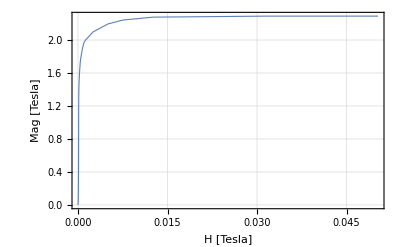

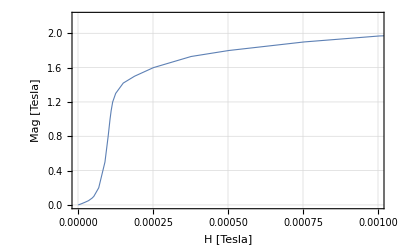

```mathematica
H = {0.8, 1.5, 2.2, 3.6, 5, 6.8, 9.8, 18, 28, 37.5, 42, 55, 71.5, 80, 85, 88, 92, 100, 120, 150, 200, 300, 400, 600, 800, 1000, 2000, 4000, 6000, 10000, 25000, 40000};

M = {0.000998995, 0.00199812, 0.00299724, 0.00499548,0.00699372, 0.00999145, 0.0149877, 0.0299774, 0.0499648, 0.0799529, 0.0999472, 0.199931, 0.49991, 0.799899, 0.999893, 1.09989, 1.19988, 1.29987, 1.41985, 1.49981, 1.59975, 1.72962, 1.7995, 1.89925, 1.96899, 1.99874,  2.09749, 2.19497, 2.24246, 2.27743, 2.28958, 2.28973};

ma =  N[Table[{H[[i]]*4*Pi*10^(-7), M[[i]]}, {i, 1, Length[H]}]];

RadPlotOptions[];
ListPlot[ma,
Joined->True,
AxesLabel->{"H [Tesla]","Mag [Tesla]"}]

ListPlot[ma,
Joined->True,
PlotRange->{{0,0.001},{0,2.2}},
AxesLabel->{"H [Tesla]","Mag [Tesla]"}]

mp=radMatSatIso[ma];
```

## Functions for odd numbers of pole (you can choose either odd or even poles)

The following function builds an array of rectangular permanent magnets with their mirror symmetric counterparts, distributes the colors, magnetic materials and sets the segmentation. The function is very generic and can be used to build almost any hybrid wiggler (without optimizing the design of terminations).

```mathematica
wig[]:=Module[{},

(* A model for odd numbers in main poles *)
(* array for up and down in z *)
For[array=1,array>=-1,array-=2,(

(* First Principal Pole p *)
p1={{0,0,array*(sp[[3]]+gapoffset)},{lp[[1]]-2*chp[[1]],lp[[2]]-2*chp[[2]]}};
p2={{0,0,array*(chp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
p3={{0,0,array*(lp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
pole0=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[pole0,npd,cp,mp];

(* side for positive and negative in y *)
For[side=1,side>=-1,side-=2,(
y=lp[[2]]/2;

For[i=1,i<=NumPer,i++,(
(* Random generator 1p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians a",i," (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Periodic Magnet 1p *)
initm={ms[[1]],side*array*ms[[2]]*(Mod[i,2]-Mod[i+1,2]),ms[[3]]};
y+=sp[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnetP1=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP1,nmd,cm,mm];
y+=lm[[2]]/4;

(* Random generator 2p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians b",i," (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Periodic Magnet 2p *)
initm={ms[[1]],side*array*ms[[2]]*(Mod[i,2]-Mod[i+1,2]),ms[[3]]};
y+=lm[[2]]/4+sp[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnetP2=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP2,nmd,cm,mm];
y+=lm[[2]]/4;

(* Periodic Pole p *)
y+=(lm[[2]]/2+lp[[2]])/2+sp[[2]];
p1={{0,side*(y),array*(sp[[3]]+gapoffset)},{lp[[1]]-2*chp[[1]],lp[[2]]-2*chp[[2]]}};
p2={{0,side*(y),array*(chp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
p3={{0,side*(y),array*(lp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
poleP=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[poleP,npd,cp,mp];
y+=lp[[2]]/2;

If[i==1,magnet1=radObjCnt[{magnetP1,magnetP2}],radObjAddToCnt[magnet1,{magnetP1,magnetP2}]];
If[i==1,pole1=radObjCnt[{poleP}],radObjAddToCnt[pole1,{poleP}]];
(*radObjAddToCnt[und,{poleP,mangetP1,magnetP2}];*)
)];

(* Random generator 3p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians before end1 (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Magnet before End pole p *)
initm={ms[[1]],side*array*ms[[2]]*(Mod[NumPer+1,2]-Mod[NumPer,2]),ms[[3]]};
y+=sp[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnet2a=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnet2a,nmd,cm,mm];

(* Random generator 4p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians before end2 (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Magnet before End pole p *)
initm={ms[[1]],side*array*ms[[2]]*(Mod[NumPer+1,2]-Mod[NumPer,2]),ms[[3]]};
y+=lm[[2]]/2+sp[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnet2b=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnet2b,nmd,cm,mm];
magnet2=radObjCnt[{magnet2a,magnet2b}];

(* End pole p *)
y+=(lm[[2]]+lep[[2]])/2+sp[[2]]+dpm[[1]];
p1={{0,side*(y),array*(sp[[3]]+gapoffset)},{lep[[1]]-2*chp[[1]],lep[[2]]-2*chp[[2]]}};
p2={{0,side*(y),array*(chp[[3]]+sp[[3]]+gapoffset)},{lep[[1]],lep[[2]]}};
p3={{0,side*(y),array*(lep[[3]]+sp[[3]]+gapoffset)},{lep[[1]],lep[[2]]}};
pole2=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[pole2,npd,cp,mp];

(* Random generator 5p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians end (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* End magnet for half size and unit model p *)
If[(NumPer!=0)&&(ending==0),initm={ms[[1]],side*array*ms[[2]]*(-Mod[NumPer,2]+Mod[NumPer+1,2]),ms[[3]]},initm={ms[[1]],side*array*ms[[2]]*(Mod[NumPer,2]-Mod[NumPer+1,2]),ms[[3]]}];
If[(NumPer==0)||(ending==0),y+=lep[[2]]/2-lm[[2]]-lep[[2]]-sp[[2]]-dpm[[1]],y+=lep[[2]]/2+sp[[2]]+dpm[[2]]];
If[(NumPer==0),y-=sp[[2]],y];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magEnd=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magEnd,nmd,cm,mm];

If[(NumPer==0),If[(side==1 && array==1),magnet=radObjCnt[{magEnd}],radObjAddToCnt[magnet,{magEnd}]],If[(side==1 && array==1),magnet=radObjCnt[{magnet1,magnet2,magEnd}],radObjAddToCnt[magnet,{magnet1,magnet2,magEnd}]]];
If[(NumPer==0),If[(side==1 && array==1),pole=radObjCnt[{pole0}],radObjAddToCnt[pole,{pole0}]],If[(array==1),If[side==1,pole=radObjCnt[{pole0,pole1,pole2}],radObjAddToCnt[pole,{pole1,pole2}]],If[side==1,radObjAddToCnt[pole,{pole0,pole1,pole2}],radObjAddToCnt[pole,{pole1,pole2}]]]];
If[(NumPer==0),poleF=radObjCnt[{pole0}],If[(array==1),If[side==1,poleF=radObjCnt[{pole0,pole1,pole2}],radObjAddToCnt[poleF,{pole1,pole2}]]]];
If[(NumPer==0),If[(side==1 && array==1),und=radObjCnt[{pole0}],radObjAddToCnt[und,{pole0}]],If[(array==1),If[side==1,und=radObjCnt[{pole0,pole1,magnet1}],radObjAddToCnt[und,{pole1,magnet1}]],If[side==1,radObjAddToCnt[und,{pole0,pole1,magnet1}],radObjAddToCnt[und,{pole1,magnet1}]]]];
If[(NumPer==0)||(ending==0),radObjAddToCnt[und,{magEnd}],radObjAddToCnt[und,{magnet2,pole2,magEnd}]];

)];
)];

y=Abs[y];

If[(NumPer==0)||(ending==0),y+=lm[[2]]/4,y+=lm[[2]]/4];
If[(NumPer==0),y+=sp[[2]],y];

undfrc=radObjCnt[{pole,magnet}];

(*undc=radObjCutMag[und,{0,0,40},{0,0,1},Frame->Lab][[1]];*)
(*Print["Total length (",NumPer*2+1," poles):    ",N[(y+lm[[2]]/4)*2,5],"  mm"];*)
totallength=N[(y+lm[[2]]/4)*2,5];
numPoles=NumPer*2+1;
und
]
```

## Functions for even numbers of pole (you can choose either odd or even poles)

The following function builds an array of rectangular permanent magnets with their mirror symmetric counterparts, distributes the colors, magnetic materials and sets the segmentation. The function is very generic and can be used to build almost any hybrid wiggler (without optimizing the design of terminations).

```mathematica
wig[]:=Module[{},

(* A model for even numbers in main poles *)
(* array for up and down in z *)
For[array=1,array>=-1,array-=2,(
(* side for positive and negative in y *)
For[side=1,side>=-1,side-=2,(
y=0;
For[i=1,i<=NumPer,i++,(
(* Random generator 1 *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians end (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Periodic Magnet 1 *)
initm={ms[[1]],array*ms[[2]]*(Mod[i,2]-Mod[i+1,2]),ms[[3]]};
If[i==1,y+=sp[[2]]/2,y+=sp[[2]]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnetP1=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP1,nmd,cm,mm];
If[i==1,y+=lm[[2]]/4,y+=lm[[2]]/4];

(* Periodic Pole p *)
y+=(lm[[2]]/2+lp[[2]])/2+sp[[2]];
p1={{0,side*(y),array*(sp[[3]]+gapoffset)},{lp[[1]]-2*chp[[1]],lp[[2]]-2*chp[[2]]}};
p2={{0,side*(y),array*(chp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
p3={{0,side*(y),array*(lp[[3]]+sp[[3]]+gapoffset)},{lp[[1]],lp[[2]]}};
poleP=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[poleP,npd,cp,mp];

(* Random generator 2 *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians end (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Periodic Magnet 2 *)
initm={ms[[1]],array*ms[[2]]*(Mod[i+1,2]-Mod[i,2]),ms[[3]]};
y+=lp[[2]]/2+sp[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnetP2=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnetP2,nmd,cm,mm];
y+=lm[[2]]/2;

If[i==1,magnet1=radObjCnt[{magnetP1,magnetP2}],radObjAddToCnt[magnet1,{magnetP1,magnetP2}]];
If[i==1,pole1=radObjCnt[{poleP}],radObjAddToCnt[pole1,{poleP}]];
(*radObjAddToCnt[und,{poleP,mangetP1,magnetP2}];*)
)];

(* Random generator 3p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians end (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* Magnet before End pole p *)
initm={ms[[1]],array*ms[[2]]*(Mod[NumPer+1,2]-Mod[NumPer,2]),ms[[3]]};
If[NumPer==0,y+=sp[[2]]/2;,y+=sp[[2]];];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magnet2=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magnet2,nmd,cm,mm];
y+=lm[[2]]/4;

(* End pole p *)
y+=(lm[[2]]/2+lep[[2]])/2+sp[[2]]+dpm[[1]];
p1={{0,side*y,array*(sp[[3]]+gapoffset)},{lep[[1]]-2*chp[[1]],lep[[2]]-2*chp[[2]]}};
p2={{0,side*y,array*(chp[[3]]+sp[[3]]+gapoffset)},{lep[[1]],lep[[2]]}};
p3={{0,side*y,array*(lep[[3]]+sp[[3]]+gapoffset)},{lep[[1]],lep[[2]]}};
pole2=radObjMltExtRtg[{p1,p2,p3},zer];
npd={np[[2]],np[[2]],np[[1]]};
fullMag[pole2,npd,cp,mp];

(* Random generator 4p *)
r=RandomVariate[NormalDistribution[1,sdr]];
theta=RandomVariate[NormalDistribution[0,sdt]]*Pi/180;
phi=RandomReal[]*2*Pi;
If[sd==0,ms={0,1,0},ms={Sin[theta]*Cos[phi], Cos[theta], Sin[theta]*Sin[phi]}];
If[sd==0,mm=RadMatNdFeB[mt], mm=RadMatNdFeB[mt*r]];
(*Print["Random radians end (",r,", ",theta,", ",phi,"), cartesian (",ms[[1]],", ",ms[[2]],", ",ms[[3]],"), norm (",Sqrt[ms[[1]]^2+ms[[2]]^2+ms[[3]]],")"];*)
(* End magnet for half size and unit model p *)
If[(NumPer!=0)&&(ending==0),initm={ms[[1]],array*ms[[2]]*(-Mod[NumPer,2]+Mod[NumPer+1,2]),ms[[3]]},initm={ms[[1]],array*ms[[2]]*(Mod[NumPer,2]-Mod[NumPer+1,2]),ms[[3]]}];
y+=lep[[2]]/2+sp[[2]]+dpm[[2]];
z1={{0,side*(y+lm[[2]]/4),array*(sp[[3]])},{lm[[1]]-2*chmk,lm[[2]]/2}};
z2={{0,side*(y+lm[[2]]/4),array*(chmk+sp[[3]])},{lm[[1]],lm[[2]]/2}};
z3={{0,side*(y+lm[[2]]/4),array*(lm[[3]]+sp[[3]])},{lm[[1]],lm[[2]]/2}};
magEnd=radObjMltExtRtg[{z1,z2,z3},initm];
nmd={nm[[2]],nm[[1]],nm[[2]]};
fullMag[magEnd,nmd,cm,mm];

If[NumPer==0,If[(side==1 && array==1),magnet=radObjCnt[{magnet2,magEnd}],radObjAddToCnt[magnet,{magnet2,magEnd}]],If[(side==1 && array==1),magnet=radObjCnt[{magnet1,magnet2,magEnd}],radObjAddToCnt[magnet,{magnet1,magnet2,magEnd}]]];
If[NumPer==0,If[(side==1 && array==1),pole=radObjCnt[{pole2,pole2}],radObjAddToCnt[pole,{pole2,pole2}]],If[(side==1 && array==1),pole=radObjCnt[{pole1,pole2}],radObjAddToCnt[pole,{pole1,pole2}]]];
If[NumPer==0,poleF=radObjCnt[{pole2,pole2}],If[(array==1),If[side==1,poleF=radObjCnt[{pole1,pole2}],radObjAddToCnt[poleF,{pole1,pole2}]]]];
If[NumPer==0,If[(side==1 && array==1),und=radObjCnt[{pole2,magnet2,magEnd}],radObjAddToCnt[und,{pole2,magnet2,magEnd}]],,If[(side==1 && array==1),und=radObjCnt[{pole1,magnet1}],radObjAddToCnt[und,{pole1,magnet1}]]];
If[(NumPer>0) && (ending==0),"",radObjAddToCnt[und,{magnet2,pole2,magEnd}]];

)];
)];

y=Abs[y];
y+=lm[[2]]/4;

undfrc=radObjCnt[{pole,magnet}];

(*undc=radObjCutMag[und,{0,0,40},{0,0,1},Frame->Lab][[1]];*)
(*Print["Total length (",NumPer*2," poles):    ",N[(y+lm[[2]]/4)*2,5],"  mm"];*)
totallength=N[(y+lm[[2]]/4)*2,5];
numPoles=NumPer*2;
und
]
```

## Create Geometry

The following instructions build an undulator with NdFeB magnets and poles  made with the material previously defined. One could also use a Radia predefined steel by replacing "mp=radMatSatIso[ma]" with "mp=RadMatAFK502[]" or "m=RadMatXc06[]" or "m=RadMatSteel42[]". See the section "How to get Help" later on to obtain the full specification of any of the material predefined in Radia .

```mathematica
radUtiDelAll[];
headers={"ME/eV", ""};

(* General Parameters: gap, # of periods, unit length, offset (not used), and ending suppresion on:0/off:1 *)
gap=15;NumPer=2;per=230;gapoffset=0;ending=1;zer={0,0,0};subDiv=2;

(* Spacing Parameters for exploded view *)
sp={0,0,gap/2};

(* Pole Parameters, lengths in x,y,z, # of subdivision, color, and chamfer *)
lp={79,(per-lm[[2]]*2)/2,61};np={subDiv,subDiv};cp={1,0,1};chp={10,0,chmk};

(* Magnet Parameters *)
lm={79,100,79};nm={subDiv,subDiv};cm={0,1,1};

(* chambers: chmp for pole, chmk for keeper *)
chmp={chp[[1]],chp[[2]]};chmk=chp[[1]];

(* End Pole Parameters *)
lep={lp[[1]],lp[[2]]-6,lp[[3]]};

(* Ending gaps: gap to end pole, gap to end mag *)
dpm={0,0};

(* Define Pole Material *)
mp=RadMatAFK502[];
(*mp=radMatSatIso[ma];*)

(* Define NdFeB with 1.2 Tesla Remanent Magnetization *)
(*mm=RadMatNdFeB[1.29];*)
mt=1.2;

(* Define Magnetization errors, if sd=0, sdr: SD in mt (frac. %), sdt: SD in theta (degrees) *)
sd=0;
sdr=0.01;
sdt=0.01;

(* Define function to assign segmentation, color, material *)
fullMag[u_,x_,y_,z_]:=(radObjDivMag[u,x];radObjDrwAtr[u,y];radMatApl[u,z]);

(* Build the Structure *)
und=wig[];

strGap=IntegerString[gap,10,3];
strPoles=IntegerString[numPoles,10,2];
strPer=IntegerString[per,10,3];
strSub=IntegerString[subDiv];
Print["Total length (",numPoles," poles): ",totallength," mm, Gap: ",strGap," mm, Period: ",strPer," mm, Subdivision: ",strSub,""]
```

Total length (5 poles): 793. mm, Gap: 015 mm, Period: 230 mm, Subdivision: 2

## Plot Geometry

The following instructions create a set of 3D graphical primitives representing the structure in space, and plot it.

```mathematica
draw=radObjDrw[und];

RadPlot3DOptions[];
Show[Graphics3D[draw]
,ViewPoint->{5,-1.5,2}
,PlotRange->All]

Export[FileNameJoin[{NotebookDirectory[],"Mag_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_3D.vtk"}], Graphics3D[draw]]
```

-Graphics3D-

E:\Program Files\Wolfram Research\Mathematica\13.0\AddOns\Applications\Radia\Examples\Mag_p05_n2_g015_3D.vtk

## Solve

The following instructions Solve for the magnetization of each sub-block which constitutes the wiggler.

```mathematica
t0=AbsoluteTime[];
re=RadSolve[und,0.0003,1000];
t1=AbsoluteTime[];

Print["Solved in : ",Round[t1-t0]," seconds"];
Print["Number of Iterations : ",re[[4]]];
Print["Average Stability of Magnetization at the last iteration : ",N[re[[1]],2]," T"];
Print["Maximum Absolute Magnetization at the last iteration : ",N[re[[2]],4]," T"];
Print["Maximum H vector at the last iteration : ",N[re[[3]],4]," T"];
Print[""];
Print["Central Field Bz(0,0,0) : ",N[If[OddQ[numPoles],radFld[und,"Bz",zer],radFld[und,"Bz",{0,-per/4,0}]],4]," T"];
(*Print["Even-pole Field Bz(0,",-per/4,",0) : ",N[radFld[und,"Bz",{0,-per/4,0}],4]," T"];*)
```

Solved in : 1 seconds

Number of Iterations : 34

Average Stability of Magnetization at the last iteration : 0.000267332 T

Maximum Absolute Magnetization at the last iteration : 2.34 T

Maximum H vector at the last iteration : 0.681667 T

Central Field Bz(0,0,0) : 1.91691 T

## Plot the Magnetic Field

```mathematica
RadPlotOptions[];
trj=Plot[radFld[und,"Bz",{0,y,0}],{y,-(NumPer+1)/1*per,(NumPer+1)/1*per}
,AxesOrigin->{0,0}
,RotateLabel->True
,FrameLabel->{"Y [mm]","Bz [T]","X = Z =  0",""}]
(*Print[trj[[1,1,1,3,1,2,1]]];*)
(*t=Table[{y, radFld[und,"Bz",{0,y,0}]},{y,-(NumPer+1)/1*per,(NumPer+1)/1*per}];*)
t=Table[trj[[1,1,1,3,1,2,1]]];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"Field_y_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>".dat"}],t]
```

```mathematica
RadPlotOptions[];
trj=Plot[radFld[und,"Bz",{x,0,0}],{x,-100,100}
,AxesOrigin->{0,0}
,RotateLabel->True
,FrameLabel->{"X [mm]","Bz [T]","Y = Z =  0",""}]
(*t=Table[{x, radFld[und,"Bz",{x,0,0}]},{x,-100,100}];*)
t=Table[trj[[1,1,1,3,1,2,1]]];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"Field_x_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>".dat"}],t]
```

## Checking the Magnetic Material

This cell presents a plot of the Magnetization vs Field Strength for the materials in use. Note that the NdFeB is anisotropic.

```mathematica
RadPlotOptions[];
Plot[radMatMvsH[pole, "mz", {0,0,hz}],{hz,-0.01,0.01}
,FrameLabel->"Pole Material "
,AxesLabel->{"H","M"}
]

Plot[
{radMatMvsH[magnet, "mz", {0,0,h}]
,radMatMvsH[magnet, "my", {0,h,0}]}
,{h,-1,1}
,FrameLabel->"NdFeB"
,AxesLabel->{"H","M"}
]
```

## Plot the Beam Trajectory

```mathematica
trj=radFldPtcTrj[und,1.2,{0,0,0,0},{-2000,2000},1001];
(*trjy=Table[x, {x, -2000, 2000, 4}];*)
trjy=trj[[All,1]];
trjx=trj[[All,2]];
t2=Table[{trjy[[z]], trjx[[z]]}, {z, 1, 1001}];
t2=Prepend[t2,headers];
Export[FileNameJoin[{NotebookDirectory[],"Trajectory_x0_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_epy"<>ToString[lep[[2]]]<>".dat"}],t2]
ListLinePlot[t2,PlotRange->{{-(NumPer+2)*(per*2/3),(NumPer+2)*(per*2/3)}, {-0.5,1.2}}
,Frame->True,FrameLabel->{"Y [mm]","Trajectory [mm]"," Z = 0 ",""}
,RotateLabel->True,GridLines->Automatic, PlotStyle->{Thickness[0.002]}]

trja=1000*trj[[All,3]];
t3=Table[{trjy[[z]], trja[[z]]}, {z, 1, 1001}];
t3=Prepend[t3,headers];
Export[FileNameJoin[{NotebookDirectory[],"Trajectory_x1_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_epy"<>ToString[lep[[2]]]<>".dat"}],t3]
ListLinePlot[t3,PlotRange->{{-(NumPer+2)*(per*2/3),(NumPer+2)*(per*2/3)},{-20, 20}}
,Frame->True,FrameLabel->{"Y [mm]","Angle [mrad]"," Z = 0 ",""}
,RotateLabel->True,GridLines->Automatic, PlotStyle->{Thickness[0.002]}]
```

## Plot the Field Integrals

```mathematica
int=Plot[radFldInt[und,"inf","ibz",{x,-1500,0},{x,1500,0}],{x,-300,300},
FrameLabel->{"X [mm]","IBz [T mm]","Z = 0",""},
RotateLabel->True]
(* which means the integral between y = -1500 to 1500 for each x ranging from -300 to 300 *)
(*Print[int[[1,1,1,3,1,2,1]]];*)
t=Table[int[[1,1,1,3,1,2,1]]];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"Fieldint_x_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_epy"<>ToString[lep[[2]]]<>".dat"}],t]
```

## Magnetization field vector

Plot the magnetization in the center of each subdivided element of the magnet.

```mathematica
RadPlot3DOptions[];
fldvec=ListVectorFieldPlot3D[radObjM[und]
,VectorHeads->True
,ColorFunction-> Hue
,PlotLabel->"Magnetization in Element # "
,ViewPoint->{3,2, 0}
,PlotRange->{All,All,All} 
,ScaleFactor->15]
(*Print[fldvec[[1,2;; ;; 5,1,1]]]*)
(*Print[fldvec[[1,1;; ;;5]]]*)
t=Table[Flatten[Join[{fldvec[[1  ,2 ;; ;; 5, 1,1]]}, {fldvec[[1  ,2 ;; ;; 5, 1,2]]},3],1]];
Export[FileNameJoin[{NotebookDirectory[],"Mag_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_vec.dat"}],t]
Export[FileNameJoin[{NotebookDirectory[],"Mag_p"<>strPoles<>"_n"<>strSub<>"_g"<>strGap<>"_vec.vtk"}],Graphics3D[fldvec]]
```

## Magnetic Force

One computes the force over the element pole induced by the whole structure. One should be cautious that the cpu time to compute the force can be very long and one must set the segmentation parameter k to the lowest values consistent with sufficient precision. Taking into account the symmetry with respect to the x axis {1,0,0} would remove the Fx component and double the Fy and Fz components.

```mathematica
k={1,1,4};
t1=AbsoluteTime[];
fr=radFldEnrFrc[poleF,und,"",k];
t2=AbsoluteTime[];
Print["{Fx, Fy, Fz} = ",N[fr,3]," Newton"];
Print ["cpu time : ",N[t2-t1,3]," seconds"];
```

## Optimizing Parameters in pole and PM dimensions

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=15;NumPer=1;per=230;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,gap/2};subDiv=2;

lp={79,(per-lm[[2]]*2)/2,61};np={subDiv,subDiv};cp={1,0,1};chp={10,0,chmk};
lm={79,100,79};nm={subDiv,subDiv};cm={0,1,1};
lep={lp[[1]],lp[[2]]-6,lp[[3]]};
chmp={chp[[1]],chp[[2]]};chmk=chp[[1]];
sd=1;
sdr=0.000001;
sdt=0.10;

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFld[und,"Bz",{0,0,0}],4]
]
For[j=1,j<=100,j++,(
(*t=Table[{y,(sp[[3]]=y;F[])},{y,5,50,5}];*)
(*t=Table[{y,(lp[[1]]=y;F[])},{y,30,100,5}];*)
(*t=Table[{y,(lm[[1]]=y;F[])},{y,50,150,5}];*)
(*t=Table[{y,(per=y;F[])},{y,100,300,20}];*)
t=Table[{y,(NumPer=y;F[])},{y,2,20,2}];
(*t=Table[{y,(np[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(nm[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(nm[[1]]=y;F[])},{y,1,5,1}];*)
(*t=Table[{y,(chp[[1]]=y;F[])},{y,1,15,1}];*)
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"maxField_gap_p"<>strPoles<>"_n"<>strSub<>"_epy"<>ToString[lep[[2]]]<>"_NP"<>ToString[j]<>".dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"NumPer","Peak Field"}]
)]
(*
t1=AbsoluteTime[];
For[j=1,j<=100,j++,(
t=Table[{y,(sdr=y;F[])},{y,0.001,0.101,0.005}];
(*t=Table[{y,(sdt=y;F[])},{y,0.01,20.01,1}];*)
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"maxField_gap_p"<>strPoles<>"_n"<>strSub<>"_epy"<>ToString[lep[[2]]]<>"_sdr"<>ToString[j]<>".dat"}],t];
t=0
)]
t2=AbsoluteTime[];
Print ["cpu time : ",N[t2-t1,3]," seconds"];
*)
```

## Field integral upon gap, distance to ending units or end side magnet height

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=15;NumPer=2;per=230;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,gap/2};subDiv=2;

lp={79,(per-lm[[2]]*2)/2,61};np={subDiv,subDiv};cp={1,0,1};chp={10,0,chmk};
lm={79,100,79};nm={subDiv,subDiv};cm={0,1,1};
lep={lp[[1]],lp[[2]]-6,lp[[3]]};
chmp={chp[[1]],chp[[2]]};chmk=10;

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldInt[und,"inf","ibz",{0,-2000,0},{0,2000,0}],3]
]

(*t=Table[{y,(gap=y;F[])},{y,5,100,5}];*)
(*t=Table[{y,(dpm[[1]]=y;F[])},{y,0,10,1}];*)
t=Table[{y,(lep[[2]]=y;F[])},{y,5,15,1}];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"fldint_p"<>strPoles<>"_n"<>strSub<>"_gap"<>strGap<>".dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"lesz","fldint"}]
```

```mathematica
(* Plot field integral in x axis upon gap, lpx, lesz *)
gap=15;NumPer=2;per=230;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,gap/2};subDiv=2;

lp={79,(per-lm[[2]]*2)/2,61};np={subDiv,subDiv};cp={1,0,1};chp={10,0,chmk};
lm={79,100,79};nm={subDiv,subDiv};cm={0,1,1};
lep={lp[[1]],lp[[2]]-6,lp[[3]]};
chmp={chp[[1]],chp[[2]]};chmk=10;

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldInt[und,"inf","ibz",{x,-2000,0},{x,2000,0}],3]
]

t=Table[{y,(x=y;F[])},{y,-20,20,2}];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"fldint_x_lesz80_gap"<>strGap<>".dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"lesz","fldint"}]
```

## Magnetic force upon gap

In this section, some iterations are made on solving and computing the peak field of the wiggler as a function of the horizontal width of the pole. The segmentation in the pole and magnet has been set to {1,1,1} resulting in a quick but inaccurate computation.

```mathematica
gap=15;NumPer=2;per=230;gapoffset=0;ending=1;zer={0,0,0};sp={0,0,gap/2};subDiv=2;

lp={79,(per-lm[[2]]*2)/2,61};np={subDiv,subDiv};cp={1,0,1};chp={10,0,chmk};
lm={79,100,79};nm={subDiv,subDiv};cm={0,1,1};
lep={lp[[1]],lp[[2]]-6,lp[[3]]};
chmp={chp[[1]],chp[[2]]};chmk=10;

F[]:=Module[{},
radUtiDelAll[];
mm=RadMatNdFeB[1.29];
mp=RadMatAFK502[];
und=wig[];
re=RadSolve[und,0.0003,1000];
N[radFldEnrFrc[poleF,und,"",{1,1,4}][[3]],3]
]

t=Table[{y,(sp[[3]]=y;F[])},{y,5,200,5}];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"force_gap.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"Gap","Force"}]

(*t=Table[{y,(NumPer=y;F[])},{y,1,5,1}];
t=Prepend[t,headers];
Export[FileNameJoin[{NotebookDirectory[],"force_pole_odd.dat"}],t];
ListPlot[t,Joined->True,AxesLabel->{"Pole","Force"}]*)
```

## How to Get Help

The following command lists all the functions defined in the Radia.exe  file.

```mathematica
?rad*
```

The following command gives the template and the description of the function  "radObjArcCur".

```mathematica
?RadPlot3DOptions
```

The following command lists all the functions defined in the Init.m file. These functions are fully written in Mathematica code

```mathematica
?Rad*
```

The following command gives the full mathematica definition of the function "RadMatAFK502" as defined in Mathematica.

```mathematica
??RadMatXc06
```